```mathematica
αcont={0.5135036591175975,0.0023893085927788557}; 
σcont={0.16963079795754127,0.00084757894486039};
ccont={-0.15964102962645102,0.0023730768366581885};
```

```mathematica
Integrate[r Sinc[k r],{r,0,rsb}]//FullSimplify
```

(1-Cos[k rsb])/k^2

```mathematica
Limit[Integrate[r^2 Sinc[k r]Exp[-a r],{r,rsb,∞}],a->0]//Simplify
```

(k rsb Cos[k rsb]-Sin[k rsb])/k^3

```mathematica
Vck[k_,rsb_,α_]:=4π α((1-Cos[k rsb])/k^2+rsb(k rsb Cos[k rsb]-Sin[k rsb])/k^3);
```

```mathematica
Reϵk[k_,mD_]:=k^2/(k^2+mD^2);
```

```mathematica
Imϵk[k_,mD_,T_]:=-π T(k mD^2)/((k^2+mD^2)^2);
```

```mathematica
(4π)/(2π)^3 k^2 Sinc[k r]Reϵk[k,mD]Vck[k,rsb,α]//FullSimplify
```

(2 k α (k+k (-1+rsb^2) Cos[k rsb]-rsb Sin[k rsb]) Sinc[k r])/((k^2+mD^2) π)

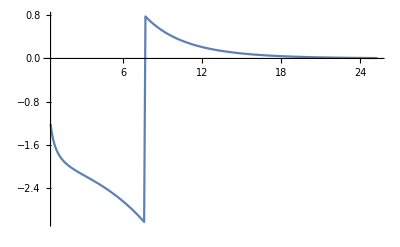

```mathematica
Block[{α=αcont[[1]],rsb=1.5/0.197,mD=0.2},DiscretePlot[NIntegrate[(2 k α (k+k (-1+rsb^2) Cos[k rsb]-rsb Sin[k rsb]) Sinc[k r])/((k^2+mD^2) π),{k,0,∞}],{r,0.1/0.197,5/0.197,0.1},Filling->None,Joined->True]]
```

```mathematica
(4π)/(2π)^3 k^2 Sinc[k r]Imϵk[k,mD,T]Vck[k,rsb,α]//FullSimplify
```

-(2 mD^2 T α (k+k (-1+rsb^2) Cos[k rsb]-rsb Sin[k rsb]) Sinc[k r])/((k^2+mD^2)^2)

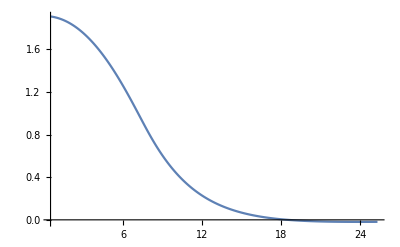

```mathematica
Block[{α=αcont[[1]],rsb=1.5/0.197,mD=0.2,T=0.155},DiscretePlot[NIntegrate[-(2 mD^2 T α (k+k (-1+rsb^2) Cos[k rsb]-rsb Sin[k rsb]) Sinc[k r])/((k^2+mD^2)^2),{k,0,∞}],{r,0.1/0.197,5/0.197,0.1},Filling->None,Joined->True]]
```